```mathematica
Module[
{many=100,deep=250,cut=200,ru,life,one,evo,data},
SeedRandom[426778];
one=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},1},deep];
Show[
ListLinePlot[
ParallelTable[
SeedRandom[2524+i];
evo=NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,3,1},1},deep];
Last/@evo
,{i,many}],
PlotRange->All,AspectRatio->1/4,Frame->True
],
ListPlot[Last/@one,PlotStyle->Black]
]
]
```

### 1D Causal graph

#### How do you separate time?

### O

```mathematica
RulePlot[CellularAutomaton[<|"RuleNumber"->40, "Neighborhood"->5, "Dimension"->2|>]]
```

RulePlot[CellularAutomaton[<|RuleNumber→40,Neighborhood→5,Dimension→2|>]]

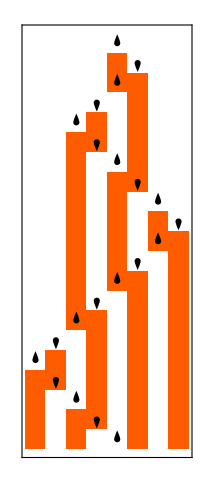

```mathematica
RulePlot[TuringMachine[2506],{1,{{},0}},20]
```

```mathematica
TuringMachine[2506]
```

TuringMachine[2506]

```mathematica
ResourceFunction["ComputationalSystemRules"][TuringMachine[2506]]
```

{{1,1}→{2,0,-1},{1,0}→{2,1,1},{2,1}→{1,0,1},{2,0}→{1,1,-1}}

```mathematica
rules={{_,x_,3}:>4+x,{_,3,_}:>0,{2,x_,_}:>4+x,{_,2,_}:>1,{5,x_,_}:>2+x,{_,5,_}:>0,{_,x_,4}:>2+x,{_,4,_}:>3,{_,x_,_}:>x};
f[{a_,b_,c_}]:={a,b,c}/. rules

explicitRules=Flatten[Table[{i,j,k}->f[{i,j,k}],{i,0,5},{j,0,5},{k,0,5}],2];
```